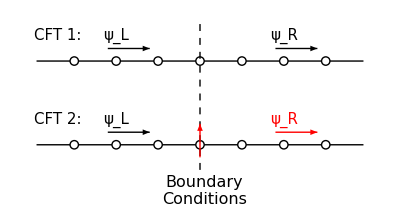

```mathematica
Show[Graphics[{
Table[Circle[{x,1},0.05],{x,0,3,0.5}],Table[Line[{{x+.05,1},{x+0.5-.05,1}}],{x,-0.5,3,0.5}],
Table[Circle[{x,0},0.05],{x,0,3,0.5}],Table[Line[{{x+.05,0},{x+0.5-.05,0}}],{x,-0.5,3,0.5}],
Text[Style["ψ_L",FontSize->15,FontFamily->"CMU Serif"],{.5,1.3}],
Text[Style["ψ_L",FontSize->15,FontFamily->"CMU Serif"],{.5,.3}],
Text[Style["ψ_R",FontSize->15,FontFamily->"CMU Serif"],{2.5,1.3}],
Red,
Text[Style["ψ_R",FontSize->15,FontFamily->"CMU Serif"],{2.5,.3}],
Black,
Arrow[{{.4,1.15},{.9,1.15}}],
Arrow[{{.4,0.15},{.9,0.15}}],
Arrow[{{2.4,1.15},{2.9,1.15}}],
Text[Style["CFT 1:",FontSize->15,FontFamily->"CMU Serif"],{-.2,1.3}],
Text[Style["CFT 2:",FontSize->15,FontFamily->"CMU Serif"],{-.2,.3}],
Red,
Arrow[{{2.4,0.15},{2.9,0.15}}],Black,Dashed,Line[{{1.5,-.3},{1.5,1.5}}],}],
Graphics[{
Text[Style["Boundary
Conditions",FontFamily->"CMU Serif Extra",FontSize->16],{1.55,-.55}],
Red,Arrow[{{1.5,-.15},{1.5,0.25}}]}]]
```

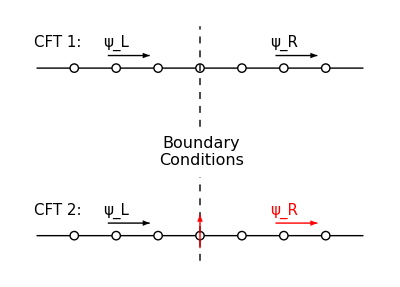

```mathematica
Show[Graphics[{
Table[Circle[{x,1},0.05],{x,0,3,0.5}],Table[Line[{{x+.05,1},{x+0.5-.05,1}}],{x,-0.5,3,0.5}],
Table[Circle[{x,-1},0.05],{x,0,3,0.5}],Table[Line[{{x+.05,-1},{x+0.5-.05,-1}}],{x,-0.5,3,0.5}],
Text[Style["ψ_L",FontSize->15,FontFamily->"CMU Serif"],{.5,1.3}],
Text[Style["ψ_L",FontSize->15,FontFamily->"CMU Serif"],{.5,-.7}],
Text[Style["ψ_R",FontSize->15,FontFamily->"CMU Serif"],{2.5,1.3}],
Red,
Text[Style["ψ_R",FontSize->15,FontFamily->"CMU Serif"],{2.5,-.7}],
Black,
Arrow[{{.4,1.15},{.9,1.15}}],
Arrow[{{.4,-1+0.15},{.9,-1+0.15}}],
Arrow[{{2.4,1.15},{2.9,1.15}}],
Text[Style["CFT 1:",FontSize->15,FontFamily->"CMU Serif Extra"],{-.2,1.3}],
Text[Style["CFT 2:",FontSize->15,FontFamily->"CMU Serif Extra"],{-.2,-0.7}],
Red,
Arrow[{{2.4,-1+0.15},{2.9,-1+0.15}}],
Black,Dashed,Line[{{1.5,-1.3},{1.5,-0.3}}],Line[{{1.5,.3},{1.5,1.5}}]}],
Graphics[{
Text[Style["Boundary
Conditions",FontFamily->"CMU Serif",FontSize->16],{1.52,0}],
Red,Arrow[{{1.5,-1.15},{1.5,-1+0.25}}]}]]
```